```mathematica
./
```

Syntax::tsntxi: "./" is incomplete; more input is needed.

```mathematica
(*Worksapce*)
$Assumptions = _ ∈ Reals;
dvec = Refine[SquaredEuclideanDistance[{px,py}+d{TrigExpand[Sin[θ+ϕ]],TrigExpand[Cos[θ+ϕ]]},D{Sin[ϕ],Cos[ϕ]}]];
Expand[dvec]
coeff = CoefficientList[Expand[dvec],{Sin[θ], Cos[θ]}];
coeff // MatrixForm
```

px^2+py^2-2 D py Cos[ϕ]+2 d py Cos[θ] Cos[ϕ]+D^2 Cos[ϕ]^2-2 d D Cos[θ] Cos[ϕ]^2+d^2 Cos[θ]^2 Cos[ϕ]^2+2 d px Cos[ϕ] Sin[θ]+d^2 Cos[ϕ]^2 Sin[θ]^2-2 D px Sin[ϕ]+2 d px Cos[θ] Sin[ϕ]-2 d py Sin[θ] Sin[ϕ]+D^2 Sin[ϕ]^2-2 d D Cos[θ] Sin[ϕ]^2+d^2 Cos[θ]^2 Sin[ϕ]^2+d^2 Sin[θ]^2 Sin[ϕ]^2

(px^2+py^2-2 D py Cos[ϕ]+D^2 Cos[ϕ]^2-2 D px Sin[ϕ]+D^2 Sin[ϕ]^2 | 2 d py Cos[ϕ]-2 d D Cos[ϕ]^2+2 d px Sin[ϕ]-2 d D Sin[ϕ]^2 | d^2 Cos[ϕ]^2+d^2 Sin[ϕ]^2
2 d px Cos[ϕ]-2 d py Sin[ϕ] | 0 | 0
d^2 Cos[ϕ]^2+d^2 Sin[ϕ]^2 | 0 | 0)

(-d^2-D^2-px^2+2 D py-py^2+R^2)/(√(4 d^2 px^2+(-2 d D+2 d py)^2))>-1

R==-d+√((D+L/(2 √3))^2+(-L/6+(2 r)/(√3))^2)

{(51632.2+311.405 px-px^2-179.79 py-py^2)/(√((-17.32 px-29.9991 py)^2+(-6227.93+29.9991 px-17.32 py)^2))>-1&&(51632.2-311.405 px-px^2-179.79 py-py^2)/(√((-6227.93-29.9991 px-17.32 py)^2+(-17.32 px+29.9991 py)^2))>-1&&(51632.2-px^2+359.58 py-py^2)/(√(1199.93 px^2+(-6227.93+34.64 py)^2))>-1,py>-(127 √3)/2&&py<127 √3+√3 px&&py<127 √3-√3 px,py<144.34&&py>-288.68+√3 px&&py>-288.68-√3 px&&py>-(127 √3)/2&&py<127 √3+√3 px&&py<127 √3-√3 px}

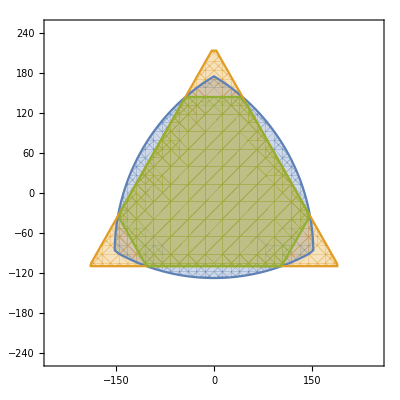

```mathematica
C1 = Simplify[coeff[[1,1]]+coeff[[1, 3]]];
A1 = coeff[[1,2]];
A2 = coeff[[2, 1]];
A = Sqrt[A1^2+A2^2];
invCond = (R^2-C1)/A >-1;
invCond /. ϕ->0

rV = 144.34;
dV = 17.32;
DV = 179.79;
LV = 381;

Req = R==Sqrt[(2r/ Sqrt[3]-L/6)^2+(D+L/(2Sqrt[3]))^2]-d
RV = 290.27;(*Sqrt[(2rV/Sqrt[3]-LV/6)^2+(DV+LV/(2Sqrt[3]))^2]-dV*)
subs = {R->RV,  r->rV, d->dV, D->DV, L->LV};
triangleCond = py>-L/(2Sqrt[3]) && py<Sqrt[3]px+L/Sqrt[3] && py<-Sqrt[3]px+L/Sqrt[3];
wsCond = {
And@@Array[invCond /.{ϕ->120# Degree}&,3], 
triangleCond,
py<r && py>Sqrt[3]px-2r&& py>-Sqrt[3]px-2r && triangleCond
}/.subs
rp = RegionPlot[wsCond, {px, -250, 250}, {py, -250, 250}]
```